```mathematica
ZPrincipal[ζ_]:=- Sqrt[π] ⅇ^(-ζ^2) Erfi[ζ];
ZDelta[ζ_]:= Sqrt[π] ⅇ^(-ζ^2);
```

Solve for the temperature ratio of the simulations

Set Physical Parameters

```mathematica
ϵT=1/50; (*Temperature ratio*)
ϵM =1/25; (*Mass ratio*)
```

Choose a system of units

```mathematica
(*mu0 := 1;epsilon0:=1;ee = 1;mi = 1;*)

ωpe=1;vTe = 0.02;
```

Set remaining physical parameters

```mathematica
ωpi:=Sqrt[ϵM]*ωpe;
cs := vTe * Sqrt[ϵM];
λe:=vTe / ωpe;
λi:=Sqrt[ϵT]*λe;
vTi:=λi *ωpi;
ke := (2 π)/λe;
felc[vz_,vy_]:=PDF[MultinormalDistribution[{1,0},{{1,0},{0,1}}],{vz,vy}];
```

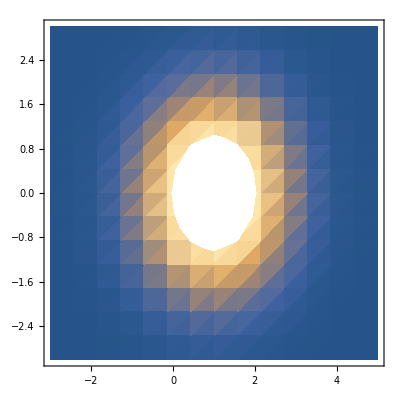

```mathematica
DensityPlot[felc[vz,vy],{vz,-3,5},{vy,-3,3}]
```

```mathematica
Plot3D[felc[vz,vy],{vz,-3,10},{vy,-3,3}]
```

-Graphics3D-

Define the longitudinal permittivity

```mathematica
ζe:=(ω-k *u)/(k *Sqrt[2]*vTe); ζi:=ω/(k*Sqrt[2]*vTi);
```

```mathematica
(*It is convenient to split epsilon into its Hermitian and anti-Hermitian parts *)

epsR:=1+(1 + ζe ZPrincipal[ζe])/(k^2 λe^2)+(1 + ζi ZPrincipal[ζi])/(k^2 λi^2);
epsI:=(ζe ZDelta[ζe])/(k^2 λe^2)+(ζi ZDelta[ζi])/(k^2 λi^2);
epsField = 1;
epsIon = (1 + ζi ZPrincipal[ζi])/(k^2 λi^2) + ⅈ (ζi ZDelta[ζi])/(k^2 λi^2);
epsElc = (1 + ζe ZPrincipal[ζe])/(k^2 λe^2)+ ⅈ (ζe ZDelta[ζe])/(k^2 λe^2);
```

## Te = 50 Ti

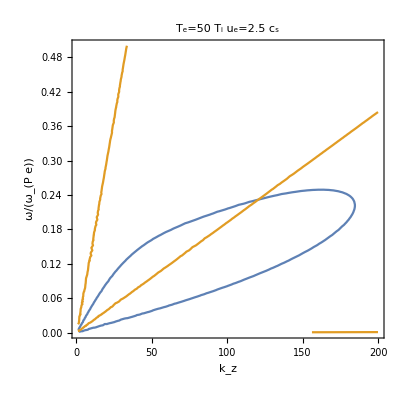

```mathematica
ϵT = 1/50;
u:=0.75vTe;
pl := ContourPlot[{0==epsR,0==epsI},{k,1,200},{ω,0.001 ωpe,0.5 ωpe}] ;
Show[     pl    ,FrameLabel->{{HoldForm[ω/Subscript[ω, P e]],None},{HoldForm[Subscript[k, z]],None}},PlotLabel->HoldForm[ Subscript[T, e] =50 Subscript[T, i]  Subscript[u, e] = 2.5 Subscript[c, s]],LabelStyle->{FontFamily->"Al Bayan",14,GrayLevel[0]}]
```

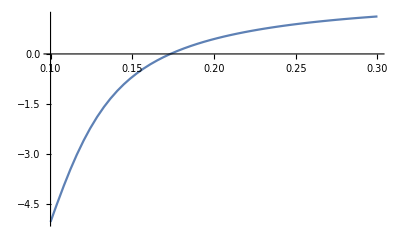

```mathematica
ϵT = 1/50;
Plot[epsR/.{k ->62.83, u-> 2.5cs},{ω,0.1, 0.3}]
```

```mathematica
Print[FindRoot[(epsR +ⅈ epsI )/.{u-> 0.75vTe,k->62.83},{ω, 0.16}]]
```

{ω→0.175517+0.0201899 ⅈ}

{ω→0.173421+0.0162447 ⅈ}

{ω→0.171824+0.0121683 ⅈ}

{ω→0.170699+0.00800923 ⅈ}

{ω→0.17002+0.00380144 ⅈ}

{ω→0.173063+0.0154381 ⅈ}

```mathematica
Sqrt[2.0]
```

1.41421

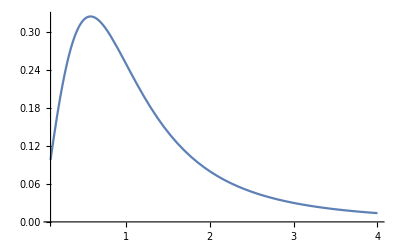

```mathematica
Plot[(1/x^3)/((1+1/x^2)^2),{x,0.1,4}]
```

```mathematica
DensityPlot[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{vz,vy}]+1/3*PDF[MultinormalDistribution[{3,0},{{1,0},{0,1}}],{vz,-3,5},{vy,-3,3}]
```

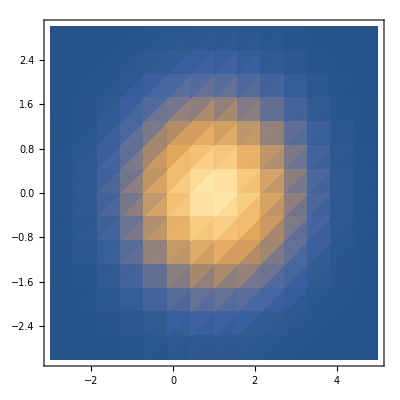

```mathematica
DensityPlot[(1-fracrun)*PDF[MultinormalDistribution[{ubulk/u,0},{{1,0},{0,1}}],{vz,vy}]+fracrun*PDF[MultinormalDistribution[{urun/u,0},{{1,0},{0,1}}],{vz,vy}],{vz,-3,5},{vy,-3,3}]
```

```mathematica
Plot3D[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{vz,vy}]+PDF[MultinormalDistribution[{2,0},{{1,0},{0,1}}],{vz,vy}],{vz,-3,5},{vy,-3,3}]
```

-Graphics3D-